```mathematica
ffCartPendulum[ICs_,n_,τ_,τ1_,A_,order_,maxIter_,InitGuess_]:=
Module[{x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,i,λ4ff0,uMax,uMin,expr,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	2/(A Cos[2 θ]+A-2)^3 (Cos[θ] (4 Sin[θ] (A λ4^2 Cos[2 θ]+4 A λ2^2+(A+2) λ4^2)-(A Cos[2 θ]-3 A+2) (A Cos[2 θ]+A-2) (A θdot^2 λ2-λ4))+A ((A-2) Cos[2 θ]+A) (A Cos[2 θ]+A-2) (λ2-θdot^2 λ4)-4 λ2 λ4 Sin[θ] (3 A Cos[2 θ]+3 A+2)),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1]; 
froot=FindRoot[eqns,sv,MaxIterations->maxIter];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
expr = 1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]);

uMax = 2;
uMin = -2;
uff0=ListInterpolation[Table[Piecewise[{{expr,uMin <= expr <= uMax},{uMin,expr <uMin},{uMax,expr > uMax}}],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0}]
```

Discrete Flow Function and Shooting Function

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
ϕh[x0_,p0_,T_,h_] := Module[{x,xStar,f,n,xFinal,output},
f[x_] := {x[[2]],-Sign[x[[4]]],0,-x[[3]]};
If[T < 0, output = Join[x0,p0],
n = IntegerPart[T/h];
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] +h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]];
];
output
]
H[x_] := 1 + x[[3]]*x[[2]] + x[[4]]*(-Sign[x[[3]]]);
ICs = {0,0};maxIter = 23;h = 0.01;
InitGuess = {0.1,0.1,20};
S[x_]:= Module[{p0,T},
p0 = Table[x[[i]],{i,1,2}];
T = x[[3]];
Flatten[{Table[ϕh[ICs,p0,T,h][[i]],{i,1,2}],H[ϕh[ICs,p0,T,h]]},1]
]
Table[If[i >= 0,
Subscript[J, i] = Subscript[J, i-1] + 1 / (Norm[Subscript[x, i] - Subscript[x, i-1]]^2)* KroneckerProduct[(S[Subscript[x, i]] - S[Subscript[x, i-1]] - Subscript[J, i-1].(Subscript[x, i] - Subscript[x, i-1])),(Subscript[x, i] - Subscript[x, i-1])];
Subscript[x, i+1] = Subscript[x, i] - Inverse[Subscript[J, i]].S[Subscript[x, i]],
Subscript[x, -1] = InitGuess;Subscript[x, 0] = InitGuess + {0.01,0.01,1}; 
Subscript[J, -1] = IdentityMatrix[3];
],{i,-1,maxIter-1}];
Subscript[J, maxIter-1]
Subscript[x, maxIter]
S[Subscript[x, maxIter]]
```

{{23.0855,-26.542,-31.3868},{-0.0598606,0.0691393,-0.635823},{-287.706,331.914,95.5205}}

{-33.338,-1.,-0.00790167}

{0,0,0.}

```mathematica
T = 2;h = 0.01;x0 = {0.2,0.4};p0 = {0.4,0.4};
final = ϕh[x0,p0,T,h]
H[final]
```

{-3.85542×10^-16,0.4,0.4,-0.4}

1.56

{{-0.515454,-4.24486,8.19013},{-0.055381,-1.20777,0.511458},{1.92663,13.6427,-0.32352}}

{1.0759,0.33,6.45202}

The Approach does not work because convexity is lost and we diverge. Need a better optimization algorithm

For Simple Convex Problems, this works

```mathematica
S[x_] := {x[[1]]^2,x[[2]]^2,x[[3]]^2};
maxIter = 100;
InitGuess = {10,10,10};
Table[If[i >= 0,
Subscript[J, i] = Subscript[J, i-1] + 1 / (Norm[Subscript[x, i] - Subscript[x, i-1]]^2)* KroneckerProduct[(S[Subscript[x, i]] - S[Subscript[x, i-1]] - Subscript[J, i-1].(Subscript[x, i] - Subscript[x, i-1])),(Subscript[x, i] - Subscript[x, i-1])];
Subscript[x, i+1] = Subscript[x, i] - Inverse[Subscript[J, i]].S[Subscript[x, i]],
Subscript[x, -1] = InitGuess;Subscript[x, 0] = InitGuess + {0.01,0.01,1}; 
Subscript[J, -1] = IdentityMatrix[3];
],{i,-1,maxIter-1}];
Subscript[J, maxIter-1]
Subscript[x, maxIter]
```

{{-39.9343,-40.9343,18.4876},{-40.9343,-39.9343,18.4876},{7.41028,7.41028,-3.87978}}

{0.582866,0.582866,0.0824899}

Try Shooting Method for Fixed Time Problem:

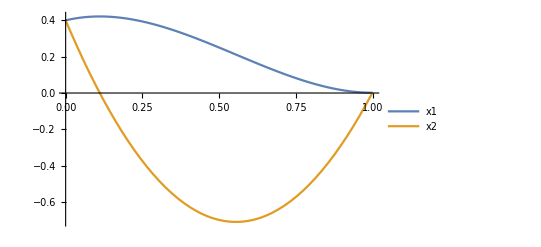

-Graphics-

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
ϕh[x0_,p0_,T_,h_] := Module[{x,xStar,f,n,xFinal,output},
f[x_] := {x[[2]],-x[[4]],0,-x[[3]]};
If[T < 0, output = Join[x0,p0],
n = IntegerPart[T/h];
xFinal = Table[If[i != -1,Subscript[xStar, i+1] = Subscript[xStar, i] +h*f[Subscript[xStar, i]],Subscript[xStar, 0] = {x0[[1]],x0[[2]],p0[[1]],p0[[2]]}],{i,-1,n-1}];
output = xFinal[[n+1]];
];
output
]
ICs = {0.4,0.4};maxIter = 5;h = 0.001;T = 1;
InitGuess = {0,0};
S[x_]:= Table[ϕh[ICs,x,T,h][[i]],{i,1,2}];
Table[If[i >= 0,
Subscript[J, i] = Subscript[J, i-1] + 1 / (Norm[Subscript[x, i] - Subscript[x, i-1]]^2)* KroneckerProduct[(S[Subscript[x, i]] - S[Subscript[x, i-1]] - Subscript[J, i-1].(Subscript[x, i] - Subscript[x, i-1])),(Subscript[x, i] - Subscript[x, i-1])];
Subscript[x, i+1] = Subscript[x, i] - Inverse[Subscript[J, i]].S[Subscript[x, i]],
Subscript[x, -1] = InitGuess;Subscript[x, 0] = InitGuess + {0.01,0.01}; 
Subscript[J, -1] = IdentityMatrix[2];
],{i,-1,maxIter-1}];
eq={x1'[t]==x2[t],x2'[t]== -λ2[t],λ1'[t] == 0,λ2'[t] == -λ1[t]};
init={x1[0]==ICs[[1]],x2[0]==ICs[[2]],λ1[0]==Subscript[x, maxIter][[1]],λ2[0]==Subscript[x, maxIter][[2]]};
{x1s,x2s,λ1s,λ2s}=NDSolveValue[{eq,init},{x1,x2,λ1,λ2},{t,0,T},Method->{"DiscontinuityProcessing"->None}];
Plot[{x1s[t],x2s[t]},{t,0,T},PlotLegends->{"x1","x2"}]
```